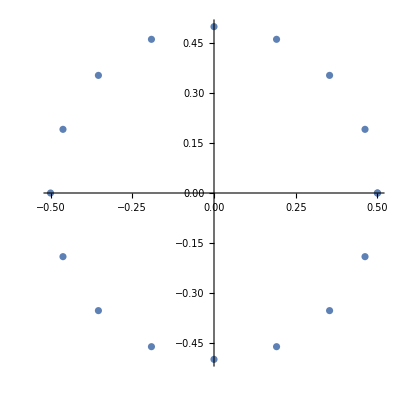

{{0.5,0.},{0.46,0.19},{0.35,0.35},{0.19,0.46},{0.,0.5},{-0.19,0.46},{-0.35,0.35},{-0.46,0.19},{-0.5,0.},{-0.46,-0.19},{-0.35,-0.35},{-0.19,-0.46},{0.,-0.5},{0.19,-0.46},{0.35,-0.35},{0.46,-0.19},{0.5,0.}}

```mathematica
r = 0.5;
t = N[Range[0,2.*Pi,Pi/8]];
x = r * Cos[t];
y = r * Sin[t];
(*ListPlot[{x,y}]*)
data = Transpose[{x,y}];
ListPlot[data, AspectRatio -> 1]
Round[data,0.01]
```

{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

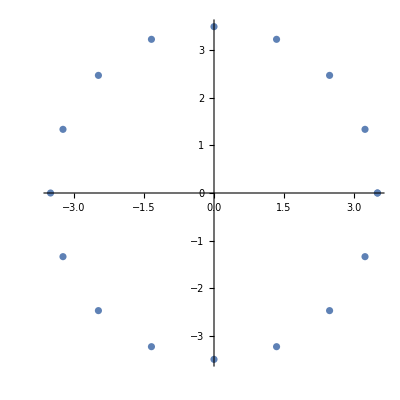

{{3.5,0.},{3.23,1.34},{2.47,2.47},{1.34,3.23},{0.,3.5},{-1.34,3.23},{-2.47,2.47},{-3.23,1.34},{-3.5,0.},{-3.23,-1.34},{-2.47,-2.47},{-1.34,-3.23},{0.,-3.5},{1.34,-3.23},{2.47,-2.47},{3.23,-1.34},{3.5,0.}}

```mathematica
rgauss = 3.5;
t = N[Range[0,2.*Pi,Pi/8]];
xgauss = rgauss * Cos[t];
ygauss = rgauss * Sin[t];
(*ListPlot[{x,y}]*)
datagauss = Transpose[{xgauss,ygauss}];
ListPlot[datagauss, AspectRatio->1]
Round[datagauss,0.01]
```

```mathematica
slope = {0.0007826239771925043,0.0009039493509247832,0.0010428497650549662} * 10.
intercept = {-0.003527443175143303,-0.008846942705030204,-0.009250214551616835} *10.
```

{0.00782624,0.00903949,0.0104285}

{-0.0352744,-0.0884694,-0.0925021}

### x - y

{451.721,417.679,320.735,175.648,4.5072,-166.634,-311.72,-408.664,-442.706,-408.664,-311.72,-166.634,4.5072,175.648,320.735,417.679,451.721}

{9.78699,157.958,283.572,367.504,396.977,367.504,283.572,157.958,9.78699,-138.384,-263.998,-347.93,-377.403,-347.93,-263.998,-138.384,9.78699}

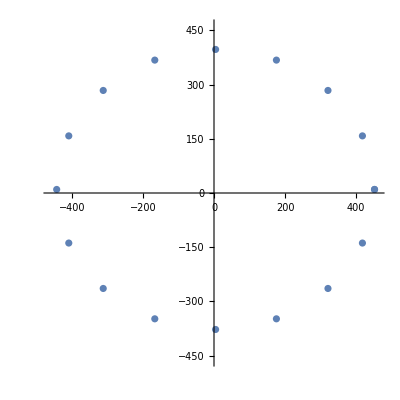

{{451.72,9.79},{417.68,157.96},{320.73,283.57},{175.65,367.5},{4.51,396.98},{-166.63,367.5},{-311.72,283.57},{-408.66,157.96},{-442.71,9.79},{-408.66,-138.38},{-311.72,-264.},{-166.63,-347.93},{4.51,-377.4},{175.65,-347.93},{320.73,-264.},{417.68,-138.38},{451.72,9.79}}

```mathematica
currentx = (xgauss - intercept[[1]])/slope[[1]]
currenty = (ygauss - intercept[[2]])/slope[[2]]
dataxy = Transpose[{currentx,currenty}];
ListPlot[dataxy,PlotRange->{{-460,460},{-460,460}}, AspectRatio->1]
Round[dataxy,0.01]
```

```mathematica
{{451.72,9.79},{417.68,157.96},{320.73,283.57},{175.65,367.5},{4.51,396.98},
{-166.63,367.50},{-311.72,283.57},{-408.66,157.96},{-442.71,9.79},
{-408.66,-138.38},{-311.72,-264.00},{-166.63,-347.93},
{4.51,-377.40},{175.65,-347.93},{320.73,-264.},{417.68,-138.38},
{451.72,9.79}}
```

### x - z

{451.721,417.679,320.735,175.648,4.5072,-166.634,-311.72,-408.664,-442.706,-408.664,-311.72,-166.634,4.5072,175.648,320.735,417.679,451.721}

{8.87013,137.306,246.188,318.941,344.489,318.941,246.188,137.306,8.87013,-119.566,-228.448,-301.201,-326.749,-301.201,-228.448,-119.566,8.87013}

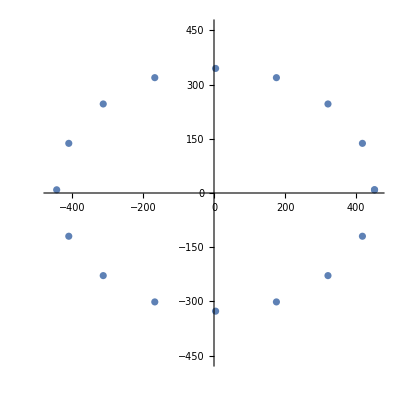

{{451.72,8.87},{417.68,137.31},{320.73,246.19},{175.65,318.94},{4.51,344.49},{-166.63,318.94},{-311.72,246.19},{-408.66,137.31},{-442.71,8.87},{-408.66,-119.57},{-311.72,-228.45},{-166.63,-301.2},{4.51,-326.75},{175.65,-301.2},{320.73,-228.45},{417.68,-119.57},{451.72,8.87}}

```mathematica
currentx = (xgauss - intercept[[1]])/slope[[1]]
currentz = (ygauss - intercept[[3]])/slope[[3]]
dataxz = Transpose[{currentx,currentz}];
ListPlot[dataxz,PlotRange->{{-460,460},{-460,460}}, AspectRatio->1]
Round[dataxz,0.01]
```

```mathematica
{{451.72,8.87},{417.68,137.31},{320.73,246.19},{175.65,318.94},{4.51,344.49},{-166.63,318.94},{-311.72,246.19},{-408.66,137.31},{-442.71,8.87},{-408.66,-119.57},{-311.72,-228.45},{-166.63,-301.2},{4.51,-326.75},
{175.65,-301.2},{320.73,-228.45},{417.68,-119.57},{451.72,8.87}}
```

### y - z

{396.977,367.504,283.572,157.958,9.78699,-138.384,-263.998,-347.93,-377.403,-347.93,-263.998,-138.384,9.78699,157.958,283.572,367.504,396.977}

{8.87013,137.306,246.188,318.941,344.489,318.941,246.188,137.306,8.87013,-119.566,-228.448,-301.201,-326.749,-301.201,-228.448,-119.566,8.87013}

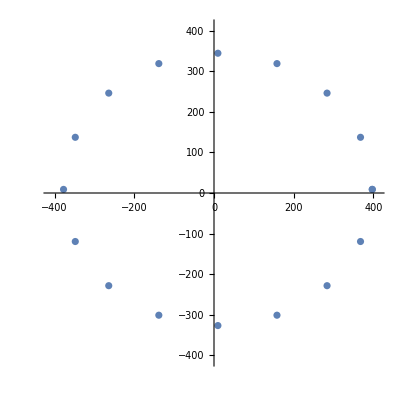

{{396.98,8.87},{367.5,137.31},{283.57,246.19},{157.96,318.94},{9.79,344.49},{-138.38,318.94},{-264.,246.19},{-347.93,137.31},{-377.4,8.87},{-347.93,-119.57},{-264.,-228.45},{-138.38,-301.2},{9.79,-326.75},{157.96,-301.2},{283.57,-228.45},{367.5,-119.57},{396.98,8.87}}

```mathematica
currenty = (xgauss - intercept[[2]])/slope[[2]]
currentz = (ygauss - intercept[[3]])/slope[[3]]
datayz = Transpose[{currenty,currentz}];
ListPlot[datayz,PlotRange->{{-410,410},{-410,410}}, AspectRatio->1]
Round[datayz,0.01]
```

```mathematica
rgauss = 3.5;
t = N[Range[0,2.*Pi,Pi/8]];
xgauss = rgauss * Cos[t];
ygauss = rgauss * Sin[t];
zgauss = 0 * t;
(*ListPlot[{x,y}]*)
datagauss = Transpose[{xgauss,ygauss, zgauss}];
ListPlot3D[datagauss, AspectRatio->1]
Round[datagauss,0.01]
Ry = RotationMatrix[45 Degree, {0,1,0}]
datarotate = datagauss.Ry
ListPlot3D[datarotate, AspectRatio->1]
Round[datarotate,0.01]
{Brotx, Broty,Brotz} = Transpose[datarotate]
```

-Graphics3D-

{{3.5,0.,0.},{3.23,1.34,0.},{2.47,2.47,0.},{1.34,3.23,0.},{0.,3.5,0.},{-1.34,3.23,0.},{-2.47,2.47,0.},{-3.23,1.34,0.},{-3.5,0.,0.},{-3.23,-1.34,0.},{-2.47,-2.47,0.},{-1.34,-3.23,0.},{0.,-3.5,0.},{1.34,-3.23,0.},{2.47,-2.47,0.},{3.23,-1.34,0.},{3.5,0.,0.}}

{{1/(√2),0,1/(√2)},{0,1,0},{-1/(√2),0,1/(√2)}}

{{2.47487,0.,2.47487},{2.28649,1.33939,2.28649},{1.75,2.47487,1.75},{0.947093,3.23358,0.947093},{1.51542×10^-16,3.5,1.51542×10^-16},{-0.947093,3.23358,-0.947093},{-1.75,2.47487,-1.75},{-2.28649,1.33939,-2.28649},{-2.47487,4.28626×10^-16,-2.47487},{-2.28649,-1.33939,-2.28649},{-1.75,-2.47487,-1.75},{-0.947093,-3.23358,-0.947093},{-4.54627×10^-16,-3.5,-4.54627×10^-16},{0.947093,-3.23358,0.947093},{1.75,-2.47487,1.75},{2.28649,-1.33939,2.28649},{2.47487,-8.57253×10^-16,2.47487}}

-Graphics3D-

{{2.47,0.,2.47},{2.29,1.34,2.29},{1.75,2.47,1.75},{0.95,3.23,0.95},{0.,3.5,0.},{-0.95,3.23,-0.95},{-1.75,2.47,-1.75},{-2.29,1.34,-2.29},{-2.47,0.,-2.47},{-2.29,-1.34,-2.29},{-1.75,-2.47,-1.75},{-0.95,-3.23,-0.95},{0.,-3.5,0.},{0.95,-3.23,0.95},{1.75,-2.47,1.75},{2.29,-1.34,2.29},{2.47,0.,2.47}}

{{2.47487,2.28649,1.75,0.947093,1.51542×10^-16,-0.947093,-1.75,-2.28649,-2.47487,-2.28649,-1.75,-0.947093,-4.54627×10^-16,0.947093,1.75,2.28649,2.47487},{0.,1.33939,2.47487,3.23358,3.5,3.23358,2.47487,1.33939,4.28626×10^-16,-1.33939,-2.47487,-3.23358,-3.5,-3.23358,-2.47487,-1.33939,-8.57253×10^-16},{2.47487,2.28649,1.75,0.947093,1.51542×10^-16,-0.947093,-1.75,-2.28649,-2.47487,-2.28649,-1.75,-0.947093,-4.54627×10^-16,0.947093,1.75,2.28649,2.47487}}

```mathematica
currentx = (Brotx - intercept[[1]])/slope[[1]]
currenty = (Broty - intercept[[2]])/slope[[2]]
currentz = (Brotz - intercept[[3]])/slope[[3]]
datacurr = Transpose[{currentx, currenty, currentz}]
datacurrround = Round[datacurr,0.01]
```

{320.735,296.663,228.114,125.522,4.5072,-116.508,-219.1,-287.649,-311.72,-287.649,-219.1,-116.508,4.5072,125.522,228.114,296.663,320.735}

{9.78699,157.958,283.572,367.504,396.977,367.504,283.572,157.958,9.78699,-138.384,-263.998,-347.93,-377.403,-347.93,-263.998,-138.384,9.78699}

{246.188,228.124,176.68,99.6879,8.87013,-81.9477,-158.939,-210.383,-228.448,-210.383,-158.939,-81.9477,8.87013,99.6879,176.68,228.124,246.188}

{{320.735,9.78699,246.188},{296.663,157.958,228.124},{228.114,283.572,176.68},{125.522,367.504,99.6879},{4.5072,396.977,8.87013},{-116.508,367.504,-81.9477},{-219.1,283.572,-158.939},{-287.649,157.958,-210.383},{-311.72,9.78699,-228.448},{-287.649,-138.384,-210.383},{-219.1,-263.998,-158.939},{-116.508,-347.93,-81.9477},{4.5072,-377.403,8.87013},{125.522,-347.93,99.6879},{228.114,-263.998,176.68},{296.663,-138.384,228.124},{320.735,9.78699,246.188}}

{{320.73,9.79,246.19},{296.66,157.96,228.12},{228.11,283.57,176.68},{125.52,367.5,99.69},{4.51,396.98,8.87},{-116.51,367.5,-81.95},{-219.1,283.57,-158.94},{-287.65,157.96,-210.38},{-311.72,9.79,-228.45},{-287.65,-138.38,-210.38},{-219.1,-264.,-158.94},{-116.51,-347.93,-81.95},{4.51,-377.4,8.87},{125.52,-347.93,99.69},{228.11,-264.,176.68},{296.66,-138.38,228.12},{320.73,9.79,246.19}}

```mathematica
Export["C:\\Users\\laima\\OneDrive - University of Latvia\\Pētījumi\\NV centri\\Kosmoss\\magnetometer_raspi\\curr_values_3D.csv", datacurrround, "CSV"]
```

C:\Users\laima\OneDrive - University of Latvia\Pētījumi\NV centri\Kosmoss\magnetometer_raspi\curr_values_3D.csv